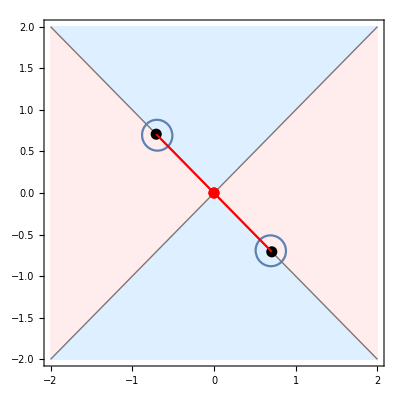

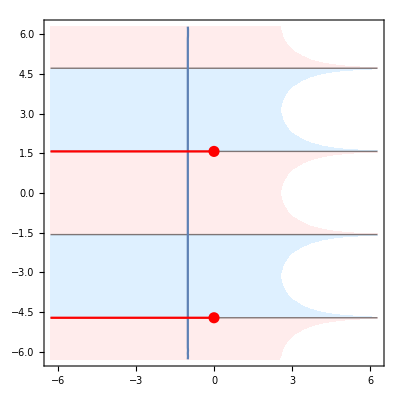

```mathematica
diag=1+I;
size=PointSize[0.02];
proc[f_,a_,b_]:=Module[{z0,cp1,cp2},
cp1=ComplexContourPlot[Re[f],{z,a-b*diag,a+b*diag},
Contours->{0},ContourShading->{LightBlue,LightPink}];
cp2=ComplexContourPlot[Abs[f]==Exp[-1],{z,a-b*diag,a+b*diag}];
Show[cp1,cp2]];
zr=Conjugate[diag]/Sqrt[2];
wr=I*Pi/2;
pz=proc[z^2+I,0,2];
pw=proc[Exp[z],0,2Pi];
bz=ComplexListPlot[{-zr,zr},PlotStyle->{Black,size}];
rz=ComplexListPlot[{0},PlotStyle->{Red,size}];
rw=ComplexListPlot[{-3wr,wr},PlotStyle->{Red,size}];
sz=ParametricPlot[ReIm[zr*t],{t,-1,1},PlotStyle->Red];
sw1=ParametricPlot[ReIm[wr-t],{t,0,2Pi},PlotStyle->Red];
sw2=ParametricPlot[ReIm[-3wr-t],{t,0,2Pi},PlotStyle->Red];
Show[pz,bz,rz,sz]
Show[pw,rw,sw1,sw2]
```